# 作业

1.1.1

1.

```mathematica
3^100
```

515377520732011331036461129765621272702107522001

2.

```mathematica
3^1000
```

1322070819480806636890455259752144365965422032752148167664920368226828597346704899540778313850608061963909777696872582355950954582100618911865342725257953674027620225198320803878014774228964841274390400117588618041128947815623094438061566173054086674490506178125480344405547054397038895817465368254916136220830268563778582290228416398307887896918556404084898937609373242171846359938695516765018940588109060426089671438864102814350385648747165832010614366132173102768902855220001

3.

```mathematica
N[%]
```

1.32207081948081×10^477

4.

```mathematica
pi = N[π,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

5.

```mathematica
ⅇ^(√163*pi/3)
```

640320.00000000060486373504901603947174181881853947577148576036659181946522182582869425363408158226464775899925470001727925679647867303997506923198495665261269396826561338913713441824901972334433096

该数是高斯勒让德算法逼近圆周率的重要中间结果。

6.

```mathematica
s = ToString[N[Pi,1000]]
StringDrop[s,2]
StringPosition[s,"999999"]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

{{764,769}}

## 1.1.2

7.

```mathematica
Sin[13π]
Log[2.1]
ⅇ^ⅈπ
```

0

0.741937

ⅇ^ⅈπ

8.

```mathematica
ToRadicals[Cos[Pi/5]]
```

1/4 (1+√5)

9.

```mathematica
FactorInteger[70612139395722186]
```

{{2,1},{3,2},{43,5},{26684839,1}}

FactorInteger[n]输出n的质数因子及其对应指数的对的列表

10.

```mathematica
f[{a_,b_}]:=a^b
Times@@Map[f,%%]
```

70612139395722186

## 1.1.3

11.

```mathematica
(x^2+2x+1)^20
Factor@Expand@%
```

(1+2 x+x^2)^20

(1+x)^40

12.

```mathematica
(x^2+2x+1)^20
Expand[(1+x)^40]
Factor[(1+x)^40]
```

(1+2 x+x^2)^20

1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40

(1+x)^40

13.

```mathematica
TrigReduce[Sin[x] Cos[y]-Cos[x] Sin[y]]
TrigExpand@%
```

Sin[x-y]

Cos[y] Sin[x]-Cos[x] Sin[y]

互为逆函数

## 1.1.4

14.

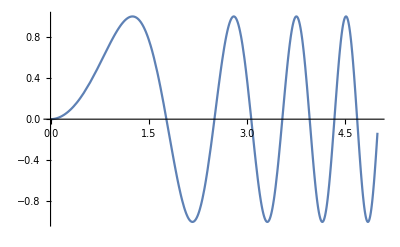

```mathematica
Plot[Sin[x^2],{x,0,5}]
```

15.

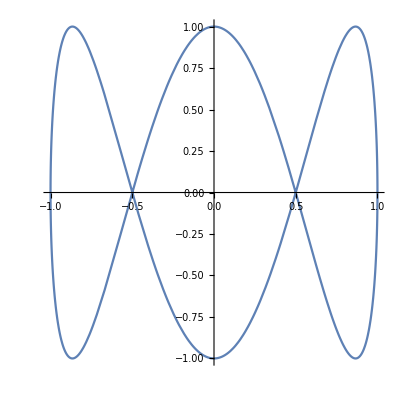

```mathematica
ParametricPlot[{Cos[x],Sin[3 x]},{x,0,2 Pi}]
```

16.

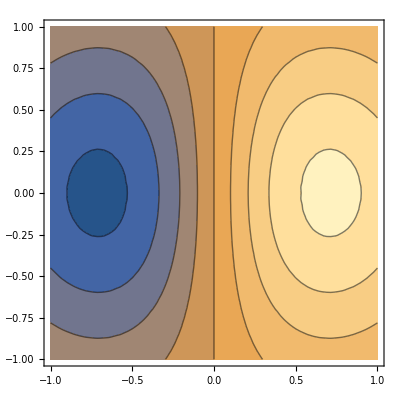

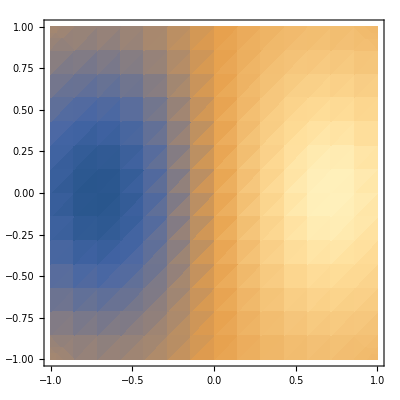

```mathematica
ContourPlot[x*ⅇ^(-x^2-y^2),{x,-1,1},{y,-1,1}]
DensityPlot[x*ⅇ^(-x^2-y^2),{x,-1,1},{y,-1,1}]
```

## 1.1.5

17.

```mathematica
∫x/(x^3-1)ⅆx
Simplify@D[%,x]
```

ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

x/(-1+x^3)

18.

```mathematica
Integrate[Sin[x]^2Cos[x]^3/x,{x,0,∞}]
N@%
```

Log[15]/16

0.169253

19.

```mathematica
Integrate[Sin@Sin@x,{x,0,1}]
N@%
```

∫_0^1 Sin[Sin[x]]ⅆx

0.430606

```mathematica
Integrate[Sin@Sin@x,{x,0,Pi}]
```

π StruveH[0,1]

## 1.1.6

20.

```mathematica
s =Solve[a x^2+b x+c == 0,x]
 Simplify[a x^2+b x+c /.s]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

{0,0}

21.

```mathematica
Clear[s]
s= N@Solve[x^3-x+1==0,x]
```

{{x→-1.32472},{x→0.662359-0.56228 ⅈ},{x→0.662359+0.56228 ⅈ}}

满足

## 1.1.7

22.

```mathematica
mat={{3.5,7.2},{-2.4,6.4}}
Inverse@mat
Eigenvalues@mat
```

{{3.5,7.2},{-2.4,6.4}}

{{0.16129,-0.181452},{0.0604839,0.0882056}}

{4.95+3.89583 ⅈ,4.95-3.89583 ⅈ}

23.

```mathematica
mat = {{a,b,c},{d,e,f},{g,h,i}}
minv = Inverse@mat
Simplify@minv.mat
```

{{a,b,c},{d,e,f},{g,h,i}}

{{(-f h+e i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(c h-b i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(-c e+b f)/(-c e g+b f g+c d h-a f h-b d i+a e i)},{(f g-d i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(-c g+a i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(c d-a f)/(-c e g+b f g+c d h-a f h-b d i+a e i)},{(-e g+d h)/(-c e g+b f g+c d h-a f h-b d i+a e i),(b g-a h)/(-c e g+b f g+c d h-a f h-b d i+a e i),(-b d+a e)/(-c e g+b f g+c d h-a f h-b d i+a e i)}}

{{((c e-b f) g)/(c e g-b f g-c d h+a f h+b d i-a e i)+(a (f h-e i))/(c e g-b f g-c d h+a f h+b d i-a e i)+(d (c h-b i))/(-c e g+b f g+c d h-a f h-b d i+a e i),((c e-b f) h)/(c e g-b f g-c d h+a f h+b d i-a e i)+(b (f h-e i))/(c e g-b f g-c d h+a f h+b d i-a e i)+(e (c h-b i))/(-c e g+b f g+c d h-a f h-b d i+a e i),((c e-b f) i)/(c e g-b f g-c d h+a f h+b d i-a e i)+(c (f h-e i))/(c e g-b f g-c d h+a f h+b d i-a e i)+(f (c h-b i))/(-c e g+b f g+c d h-a f h-b d i+a e i)},{(d (c g-a i))/(c e g-b f g-c d h+a f h+b d i-a e i)+((c d-a f) g)/(-c e g+b f g+c d h-a f h-b d i+a e i)+(a (f g-d i))/(-c e g+b f g+c d h-a f h-b d i+a e i),(e (c g-a i))/(c e g-b f g-c d h+a f h+b d i-a e i)+((c d-a f) h)/(-c e g+b f g+c d h-a f h-b d i+a e i)+(b (f g-d i))/(-c e g+b f g+c d h-a f h-b d i+a e i),(f (c g-a i))/(c e g-b f g-c d h+a f h+b d i-a e i)+((c d-a f) i)/(-c e g+b f g+c d h-a f h-b d i+a e i)+(c (f g-d i))/(-c e g+b f g+c d h-a f h-b d i+a e i)},{((b d-a e) g)/(c e g-b f g-c d h+a f h+b d i-a e i)+(a (e g-d h))/(c e g-b f g-c d h+a f h+b d i-a e i)+(d (b g-a h))/(-c e g+b f g+c d h-a f h-b d i+a e i),((b d-a e) h)/(c e g-b f g-c d h+a f h+b d i-a e i)+(b (e g-d h))/(c e g-b f g-c d h+a f h+b d i-a e i)+(e (b g-a h))/(-c e g+b f g+c d h-a f h-b d i+a e i),(c (e g-d h))/(c e g-b f g-c d h+a f h+b d i-a e i)+((b d-a e) i)/(c e g-b f g-c d h+a f h+b d i-a e i)+(f (b g-a h))/(-c e g+b f g+c d h-a f h-b d i+a e i)}}

24.

```mathematica
rand = RandomReal[{1,9},{3,3}]
Part[rand,2,2]=x
i = Inverse@rand
N@i /.x->1
```

{{2.92921,1.95607,4.79411},{1.37481,8.88215,7.86173},{6.96256,7.02132,1.50302}}

x

{{(-55.1997+1.50302 x)/(-12.3852-28.9766 x),30.7209/(-12.3852-28.9766 x),(15.3781-4.79411 x)/(-12.3852-28.9766 x)},{52.6714/(-12.3852-28.9766 x),-28.9766/(-12.3852-28.9766 x),-16.4377/(-12.3852-28.9766 x)},{(9.65299-6.96256 x)/(-12.3852-28.9766 x),-6.94766/(-12.3852-28.9766 x),(-2.68923+2.92921 x)/(-12.3852-28.9766 x)}}

{{1.29822,-0.742737,-0.255889},{-1.27343,0.700565,0.397413},{-0.0650463,0.167973,-0.00580203}}

## 1.1.8

25.

```mathematica
is = Table[i!,{i,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

26.

```mathematica
data = N@Log@is
```

{0.,0.693147,1.79176,3.17805,4.78749,6.57925,8.52516,10.6046,12.8018,15.1044}

27.

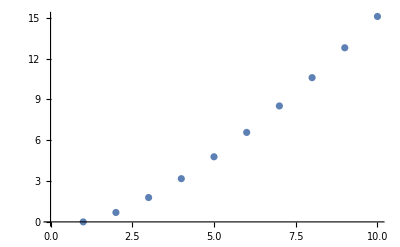

```mathematica
p1 = ListPlot@data
```

28.

-0.959735+0.685904 x+0.0933464 x^2

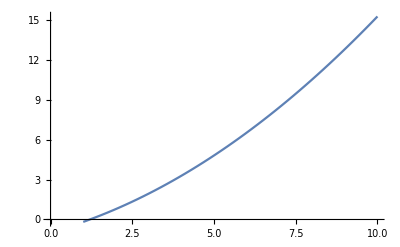

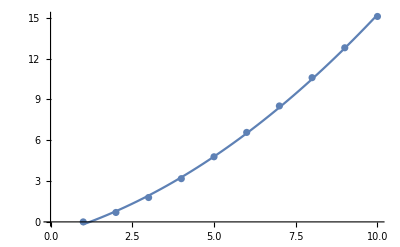

```mathematica
fit= Fit[data,{1,x,x^2},x]
p2 = Plot[fit,{x,1,10}, PlotRange->Automatic]
Show[p1,p2]
```

29.

```mathematica
Animate[Plot[Sin[a x],{x,0,2 Pi},PlotRange->{{0,2 Pi},{-1,1}}],{a,1,5}]
```

```mathematica
Animate[Plot3D[Sin[a x+b y],{x,0,2 Pi},{y,0,2 Pi},PlotRange->{{0,2 Pi},{0,2 Pi},{-1,1}}],{a,1,5},{b,1,5}]
```

30.

```mathematica
countryEntity=Entity["Country","UnitedStates"]
img=EntityValue[countryEntity,"FlagImage"]
ImageShow[img]
grayImg=ColorConvert[img,"Grayscale"]
smoothImg=GaussianFilter[img,5]
```

United States

-Graphics-

ImageShow[-Graphics-]

-Graphics-

-Graphics-